# Example Usage of Saddle Point Calculator

## Importing things

```mathematica
(* Import LV1, LVn, and Eigenfun *)
dir=If[$InputFileName!="",DirectoryName[$InputFileName],NotebookDirectory[]]; (*Current directory*)
srcdir = FileNameJoin[{ParentDirectory[dir], "src","mma"}] ;
If[MemberQ[$Path,srcdir],0,AppendTo[$Path,srcdir]];(*This import can only work if the current notebook file is saved under examples/*)
Get["LV1.wl"];
Get["LVn.wl"];
Get["Eigenfun.wl"];
```

## Analyze 1D Saddle Points

```mathematica
Ham1A[z_]:=+(-0.11020-0.01730I) z^(-2)+(+0.31890-0.32440I) z^(-1)+(-0.19120-1.89980I) z+(+0.38560+0.34600I) z^2 (*Define a Hamiltonian, this is model 1A*)
(* For any Hamiltonian defined in Python, use the to_mathematica() function to convert it. *)
```

```mathematica
(*One also needs the "Heq" and "Hmat" format, to give them to different functions*)
Heq1A[z_,l_]:= l-Ham1A[z]
Hmat1A[z_]:={{Ham1A[z]}}
```

```mathematica
SPS1[Heq1A](* Find its saddle points *)
```

{{-0.489723-0.301696 ⅈ,-0.897123+2.19844 ⅈ},{0.065639+0.390903 ⅈ,0.608155-0.826827 ⅈ},{0.526267-0.0897442 ⅈ,0.211561-1.61002 ⅈ},{1.25968+1.24197 ⅈ,1.0467-1.63076 ⅈ}}

```mathematica
SPFlows1[Hmat1A] (* Get its saddle point informations *)
```

Saddle Points:

z | E | lambda | winding | 1/Sqrt[I H''[z]] | Rvecs | Lvecs
-0.489723-0.301696 ⅈ | -0.897123+2.19844 ⅈ | 2.19844 | -1 | 0.0964162-0.275939 ⅈ | {{1}} | {{1}}
0.065639+0.390903 ⅈ | 0.608155-0.826827 ⅈ | -0.826827 | 1 | -0.217081-0.149099 ⅈ | {{1}} | {{1}}
0.526267-0.0897442 ⅈ | 0.211561-1.61002 ⅈ | -1.61002 | 0 | 0.+0. ⅈ | {{1}} | {{1}}
1.25968+1.24197 ⅈ | 1.0467-1.63076 ⅈ | -1.63076 | 0 | 0.+0. ⅈ | {{1}} | {{1}}

```mathematica
Ham1C[z_]:=+(-0.04550-0.93050I) z+(+0.39250+2.09550I) z^(-1)+(+0.11200+0.09550I) z^2+(-0.08800+1.08450I) z^(-2)
Heq1C[z_,l_]:= l-Ham1C[z]
Hmat1C[z_]:={{Ham1C[z]}}
```

```mathematica
sps1c = SPS1[Heq1C]
```

{{-0.76941-0.137738 ⅈ,-0.535217-0.0349982 ⅈ},{0.189555-1.3985 ⅈ,-3.01068-0.417068 ⅈ},{2.84736+1.87952 ⅈ,1.62663-0.606524 ⅈ},{-0.0989853+1.96169 ⅈ,2.48687-0.942526 ⅈ}}

```mathematica
SPFlows1[Hmat1C]
```

Saddle Points:

z | E | lambda | winding | 1/Sqrt[I H''[z]] | Rvecs | Lvecs
-0.76941-0.137738 ⅈ | -0.535217-0.0349982 ⅈ | -0.0349982 | -1 | 0.0903557-0.322563 ⅈ | {{1}} | {{1}}
0.189555-1.3985 ⅈ | -3.01068-0.417068 ⅈ | -0.417068 | -1 | 0.371296-0.534495 ⅈ | {{1}} | {{1}}
2.84736+1.87952 ⅈ | 1.62663-0.606524 ⅈ | -0.606524 | 1 | -0.943354+1.3149 ⅈ | {{1}} | {{1}}
-0.0989853+1.96169 ⅈ | 2.48687-0.942526 ⅈ | -0.942526 | 1 | -0.16385-1.07153 ⅈ | {{1}} | {{1}}

```mathematica
z1cSP = z/.Solve[Ham1C[z] == sps1c[[1,2]],z](* Get the roots z at saddle points energy *)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-0.76941-0.137738 ⅈ,-0.76941-0.137738 ⅈ,1.66934-0.555463 ⅈ,4.20653+5.44087 ⅈ}

```mathematica
Hmat1D[z_] := {{+(-0.27600-0.59600I) z^(-3)+(-0.19400+0.31600I) z^(-2)+(-0.74400-0.63400I) z^(-1)+(+0.31500-0.55000I)+(+0.21700+0.43400I) z+(-0.34600-0.48800I) z^2+(+0.59100-0.81800I) z^3,+(+0.00800+0.97900I) z^(-3)+(+0.77700+0.99600I) z^(-2)+(-0.54000-0.47400I) z^(-1)+(-0.71500-0.37000I)+(+0.36700+0.55400I) z+(-0.31700+0.46400I) z^2+(+0.05300+0.44600I) z^3},{+(+0.79600+0.60700I) z^(-3)+(-0.67900-0.85700I) z^(-2)+(-0.10700+0.12900I) z^(-1)+(+0.50000+0.81600I)+(-0.17700+0.17900I) z+(-0.19100-0.55800I) z^2+(-0.85700+0.75500I) z^3,+(-0.81600-0.60100I) z^(-3)+(-0.76900+0.99800I) z^(-2)+(+0.34000-0.10900I) z^(-1)+(-0.28200+0.58300I)+(-0.69400-0.54400I) z+(+0.43700+0.94700I) z^2+(-0.07400+0.90700I) z^3}}
Heq1D[z_,l_]:=Evaluate@CharacteristicPolynomial[Hmat1D[z],l]
```

```mathematica
SPFlows1[Hmat1D]
```

Saddle Points:

z | E | lambda | winding | 1/Sqrt[I H''[z]] | Rvecs | Lvecs
-1.17776+0.00152067 ⅈ | 0.8289+3.07156 ⅈ | 3.07156 | 1 | -0.121882-0.244892 ⅈ | {{0.187388+0.233932 ⅈ,-0.382977-0.873779 ⅈ}} | {{-0.000702741+0.691319 ⅈ,-0.587434-0.420711 ⅈ}}
-1.1004-0.420043 ⅈ | 1.21034+2.86317 ⅈ | 2.86317 | -1 | 0.277514-0.0766499 ⅈ | {{0.126074+0.227856 ⅈ,-0.620004-0.740123 ⅈ}} | {{0.0852776+0.323993 ⅈ,-0.580283+0.742312 ⅈ}}
0.918906+0.243414 ⅈ | -2.71715+2.83334 ⅈ | 2.83334 | -1 | 0.0719481+0.191024 ⅈ | {{0.166563+0.323851 ⅈ,-0.160014+0.917482 ⅈ}} | {{-0.0888117-0.105664 ⅈ,-0.947135+0.289624 ⅈ}}
0.726127+0.725761 ⅈ | -0.00297961+2.2626 ⅈ | 2.2626 | 1 | -0.130754+0.0575512 ⅈ | {{0.233294+0.889804 ⅈ,0.0767654-0.384616 ⅈ}} | {{0.40559+0.538646 ⅈ,-0.439701-0.593313 ⅈ}}
-0.814877+0.329657 ⅈ | 0.96699+1.99943 ⅈ | 1.99943 | -1 | 0.0355668-0.217951 ⅈ | {{-0.625108+0.0510803 ⅈ,-0.208025+0.750571 ⅈ}} | {{-0.824968+0.322623 ⅈ,-0.122253-0.447656 ⅈ}}
0.628144+0.0557166 ⅈ | -3.23169+1.96534 ⅈ | 1.96534 | 0 | 0.+0. ⅈ | {{-0.254037+0.735091 ⅈ,-0.429349+0.459093 ⅈ}} | {{-0.263857+0.226068 ⅈ,-0.806194-0.478877 ⅈ}}
-0.575835+0.955619 ⅈ | -0.882976+1.39304 ⅈ | 1.39304 | 1 | -0.196522-0.159121 ⅈ | {{-0.720251-0.190602 ⅈ,-0.653539+0.133402 ⅈ}} | {{-0.510078-0.494013 ⅈ,-0.258779-0.654832 ⅈ}}
0.0655393+0.898357 ⅈ | -1.92028+1.22187 ⅈ | 1.22187 | 1 | -0.1391+0.249425 ⅈ | {{-0.838545-0.129271 ⅈ,-0.339948+0.405669 ⅈ}} | {{0.845565+0.160547 ⅈ,0.0690142+0.504461 ⅈ}}
0.417878-0.951073 ⅈ | -0.738959+1.13005 ⅈ | 1.13005 | -1 | 0.143085+0.108479 ⅈ | {{-0.265545-0.830862 ⅈ,-0.394853+0.288524 ⅈ}} | {{-0.0151386+0.661641 ⅈ,-0.198595-0.722884 ⅈ}}
-0.159863-0.93776 ⅈ | -2.81468+1.07012 ⅈ | 1.07012 | -1 | 0.110764-0.169414 ⅈ | {{0.388223-0.0507038 ⅈ,-0.702094-0.594791 ⅈ}} | {{0.351191+0.0221531 ⅈ,-0.32831+0.876577 ⅈ}}
-1.03091+0.57603 ⅈ | -2.61295+0.596394 ⅈ | 0.596394 | 1 | -0.214085-0.0698875 ⅈ | {{-0.491196+0.336699 ⅈ,-0.729359-0.336742 ⅈ}} | {{-0.631939+0.260759 ⅈ,-0.0681885+0.726642 ⅈ}}
0.518133+0.485855 ⅈ | -0.7762+0.532893 ⅈ | 0.532893 | 1 | -0.231786-0.000463697 ⅈ | {{-0.486583-0.786748 ⅈ,-0.306457-0.224387 ⅈ}} | {{0.267654+0.672605 ⅈ,-0.434556+0.535839 ⅈ}}
0.682033+0.562066 ⅈ | -0.688972+0.459798 ⅈ | 0.459798 | -1 | 0.00616508-0.203534 ⅈ | {{0.0190216-0.892854 ⅈ,-0.217199-0.394049 ⅈ}} | {{-0.400025-0.643616 ⅈ,-0.143979-0.636403 ⅈ}}
-0.597953-0.264782 ⅈ | 1.73212+0.146698 ⅈ | 0.146698 | 0 | 0.+0. ⅈ | {{-0.0913525-0.488438 ⅈ,-0.857934+0.13051 ⅈ}} | {{-0.232238+0.870176 ⅈ,-0.24307+0.360244 ⅈ}}
-0.450344-0.296357 ⅈ | 1.67287+0.0494934 ⅈ | 0.0494934 | 0 | 0.+0. ⅈ | {{-0.273542-0.0741781 ⅈ,-0.819921+0.497396 ⅈ}} | {{-0.807529+0.327944 ⅈ,-0.489291-0.0307311 ⅈ}}
0.716909-0.599698 ⅈ | -0.696522-0.260152 ⅈ | -0.260152 | 1 | -0.132884+0.0778823 ⅈ | {{-0.396185-0.715921 ⅈ,-0.532038+0.217785 ⅈ}} | {{-0.659526-0.169696 ⅈ,-0.43509-0.589004 ⅈ}}
-1.40487-0.172386 ⅈ | -0.615571-0.734605 ⅈ | -0.734605 | -1 | 0.121787-0.171024 ⅈ | {{0.664618+0.23885 ⅈ,-0.318839+0.63212 ⅈ}} | {{-0.876463-0.276931 ⅈ,-0.346997-0.186321 ⅈ}}
-0.231268-0.74282 ⅈ | 3.22308-1.67702 ⅈ | -1.67702 | -1 | 0.244472+0.069898 ⅈ | {{-0.760489+0.324201 ⅈ,-0.328049-0.457093 ⅈ}} | {{-0.822169+0.408849 ⅈ,-0.264779+0.294573 ⅈ}}
-0.491362-0.619203 ⅈ | 2.99277-1.86625 ⅈ | -1.86625 | 0 | 0.+0. ⅈ | {{-0.0328135+0.710831 ⅈ,-0.53761-0.452347 ⅈ}} | {{-0.954493+0.173119 ⅈ,-0.231763+0.0725207 ⅈ}}
0.633724-0.698838 ⅈ | 1.18947-1.87262 ⅈ | -1.87262 | -1 | 0.0921526+0.202449 ⅈ | {{-0.709747+0.194761 ⅈ,-0.107735-0.668371 ⅈ}} | {{-0.424769+0.0782485 ⅈ,-0.00685502+0.901888 ⅈ}}
0.485726-0.808024 ⅈ | 1.12693-1.95259 ⅈ | -1.95259 | -1 | 0.190527-0.177286 ⅈ | {{-0.470812+0.625052 ⅈ,-0.61623+0.088925 ⅈ}} | {{-0.19555-0.394111 ⅈ,-0.89764-0.026062 ⅈ}}
0.975625-0.235459 ⅈ | -0.309609-3.55155 ⅈ | -3.55155 | -1 | 0.199536-0.0244773 ⅈ | {{0.735654+0.575194 ⅈ,-0.255343-0.250528 ⅈ}} | {{0.806643+0.367132 ⅈ,-0.367013-0.282565 ⅈ}}
-0.496971+1.23614 ⅈ | 1.64914-3.6615 ⅈ | -3.6615 | 0 | 0.+0. ⅈ | {{0.408209+0.312275 ⅈ,-0.659389-0.548686 ⅈ}} | {{0.747679-0.383992 ⅈ,-0.529287-0.115675 ⅈ}}
0.0878395+1.20289 ⅈ | 3.20374-4.0642 ⅈ | -4.0642 | 1 | -0.145407-0.166085 ⅈ | {{-0.075846+0.322943 ⅈ,-0.874099-0.354832 ⅈ}} | {{-0.0112289-0.585601 ⅈ,-0.795504+0.155302 ⅈ}}

## Analyze 2D Saddle Points

```mathematica
Ham2C[z1_,z2_]:=+(+0.79612-0.46847I) z2^(-2)+(-0.14319-1.13573I) z1^(-1) z2^(-1)+(-1.25526+0.99132I) z2^(-1)+(+0.16527-0.46118I) z1 z2^(-1)+(-0.16304+0.36107I) z1^(-2)+(+0.90965-0.11266I) z1^(-1)+(-0.67856-0.38606I)+(-0.05237+1.53487I) z1+(+1.27515+0.33170I) z1^2+(-1.22052-0.90335I) z1^(-1) z2+(-1.15259+0.93853I) z2+(-0.91702+0.47410I) z1 z2+(+0.33465+0.92890I) z2^2
Hmat2C[z1_,z2_]:={{Ham2C[z1,z2]}}
Heq2C[zs_,l_]:=Quiet[l-Ham2C[zs[[1]],zs[[2]]]]
```

```mathematica
SPS[Heq2C,2]
```

{{{0.698515+0.286597 ⅈ,0.409265-2.06911 ⅈ},0.194417+4.51445 ⅈ},{{-0.915089-0.605904 ⅈ,0.725777-0.0750169 ⅈ},1.44027+3.93508 ⅈ},{{-0.811667-0.445848 ⅈ,0.321368+0.609364 ⅈ},-0.27681+3.40648 ⅈ},{{0.624475-0.0340357 ⅈ,0.202826-0.640961 ⅈ},0.181946+2.7418 ⅈ},{{0.930153+0.114037 ⅈ,-0.859333+0.127827 ⅈ},6.97079+2.16753 ⅈ},{{-0.025597-0.498463 ⅈ,-0.62535+0.589439 ⅈ},1.93379+0.784951 ⅈ},{{0.437902-0.86433 ⅈ,0.778735-0.50542 ⅈ},1.18645+0.669527 ⅈ},{{-0.155579+0.783586 ⅈ,0.610093-0.25713 ⅈ},-5.45297+0.505434 ⅈ},{{-0.612386-0.831231 ⅈ,-1.17694+0.81061 ⅈ},1.08776+0.219864 ⅈ},{{0.0938415+0.754319 ⅈ,0.511624+0.459346 ⅈ},-7.26927-0.589032 ⅈ},{{-0.0804979-0.25188 ⅈ,-0.584227-0.658836 ⅈ},-4.89195-0.725101 ⅈ},{{0.804553-0.769673 ⅈ,0.49018+0.711169 ⅈ},-2.62976-1.39512 ⅈ},{{0.291376+0.170325 ⅈ,0.647709+0.503766 ⅈ},-6.14358-1.66933 ⅈ},{{-0.663789-1.20328 ⅈ,-0.563565-0.983664 ⅈ},-2.43531-2.8538 ⅈ},{{-0.635609+0.835615 ⅈ,-1.13287+0.484786 ⅈ},1.55979-5.96196 ⅈ},{{-0.766937+0.462409 ⅈ,-0.676899-1.29188 ⅈ},-3.28848-6.45886 ⅈ}}

Saddle Points:

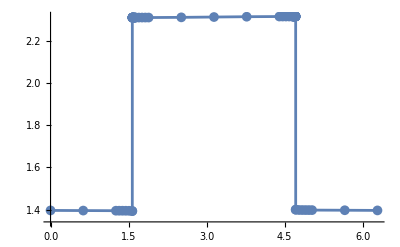
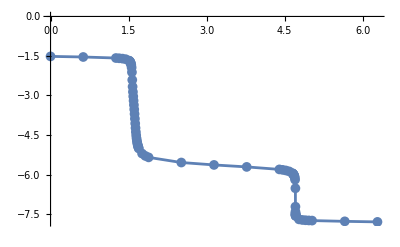
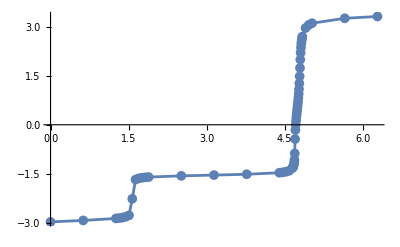
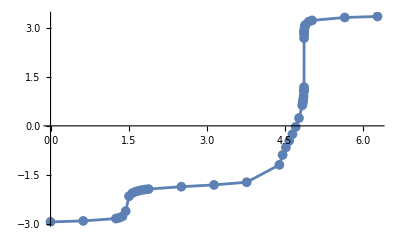
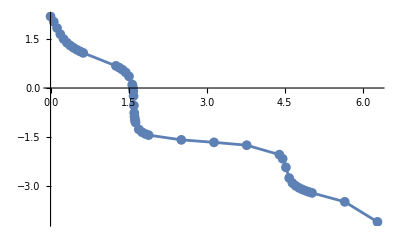
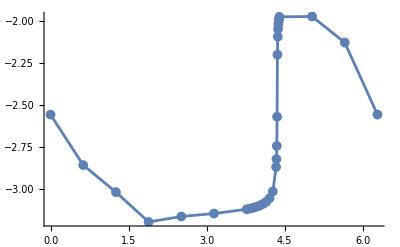
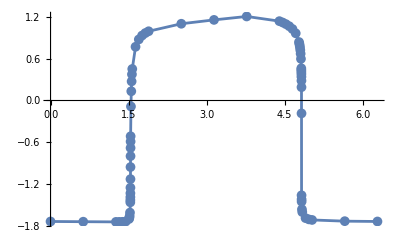
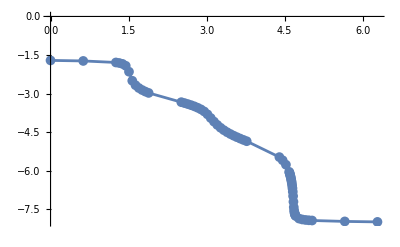
z | H[z] | lambda | wind | phases
{0.698515+0.286597 ⅈ,0.409265-2.06911 ⅈ} | 0.194417+4.51445 ⅈ | 4.51445 | 0 | -Graphics-
{-0.915089-0.605904 ⅈ,0.725777-0.0750169 ⅈ} | 1.44027+3.93508 ⅈ | 3.93508 | -1 | -Graphics-
{-0.811667-0.445848 ⅈ,0.321368+0.609364 ⅈ} | -0.27681+3.40648 ⅈ | 3.40648 | 1 | -Graphics-
{0.624475-0.0340357 ⅈ,0.202826-0.640961 ⅈ} | 0.181946+2.7418 ⅈ | 2.7418 | 1 | -Graphics-
{0.930153+0.114037 ⅈ,-0.859333+0.127827 ⅈ} | 6.97079+2.16753 ⅈ | 2.16753 | -1 | -Graphics-
{-0.025597-0.498463 ⅈ,-0.62535+0.589439 ⅈ} | 1.93379+0.784951 ⅈ | 0.784951 | 0 | -Graphics-
{0.437902-0.86433 ⅈ,0.778735-0.50542 ⅈ} | 1.18645+0.669527 ⅈ | 0.669527 | 0 | -Graphics-
{-0.155579+0.783586 ⅈ,0.610093-0.25713 ⅈ} | -5.45297+0.505434 ⅈ | 0.505434 | -1 | -Graphics-
{-0.612386-0.831231 ⅈ,-1.17694+0.81061 ⅈ} | 1.08776+0.219864 ⅈ | 0.219864 | 1 | -Graphics-
{0.0938415+0.754319 ⅈ,0.511624+0.459346 ⅈ} | -7.26927-0.589032 ⅈ | -0.589032 | 1 | -Graphics-
{-0.0804979-0.25188 ⅈ,-0.584227-0.658836 ⅈ} | -4.89195-0.725101 ⅈ | -0.725101 | 0 | -Graphics-
{0.804553-0.769673 ⅈ,0.49018+0.711169 ⅈ} | -2.62976-1.39512 ⅈ | -1.39512 | 0 | -Graphics-
{0.291376+0.170325 ⅈ,0.647709+0.503766 ⅈ} | -6.14358-1.66933 ⅈ | -1.66933 | -1 | -Graphics-
{-0.663789-1.20328 ⅈ,-0.563565-0.983664 ⅈ} | -2.43531-2.8538 ⅈ | -2.8538 | -1 | -Graphics-
{-0.635609+0.835615 ⅈ,-1.13287+0.484786 ⅈ} | 1.55979-5.96196 ⅈ | -5.96196 | 0 | -Graphics-
{-0.766937+0.462409 ⅈ,-0.676899-1.29188 ⅈ} | -3.28848-6.45886 ⅈ | -6.45886 | 0 | -Graphics-

```mathematica
SPFlows[Heq2C,2]
```